```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
<<MaTeX`;
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
a[x_,y_]:={Thickness[0.005],Arrowheads[0.075],Arrow[{{x,-y/2},{x,y/2}}]};
d[x_,y_,r_,color_,ef_:{Thickness[0.005],Black}]:={EdgeForm[ef],Lighter[color],Disk[{x,y},r]};
rc[x_,y_,r_,color_,ef_:{Black}]:={EdgeForm[ef],Lighter[color],Rectangle[{x-hw,y-hw},{x+hw,y+hw}](*Disk[{x,y},r]*)};
e[x_,y_,dx_,dy_,ef_:{White}]:={EdgeForm[ef],eraserColor,Rectangle[{x-dx/2,y-dy/2},{x+dx/2,y+dy/2}]};
```

```mathematica
holeFillingColor=White;(*Darker[Blend[{Blue,Darker[Cyan]},0.5]];*)
magnonFillingColor=Gray;(*Darker[Red];*)
eraserColor=White;
h=2;
hw=0.2;
r=0.25;
```

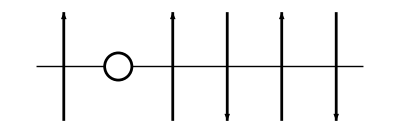

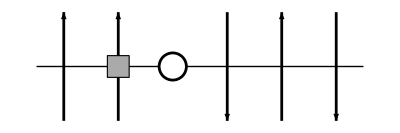

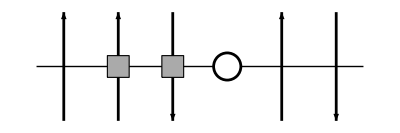

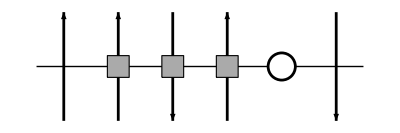

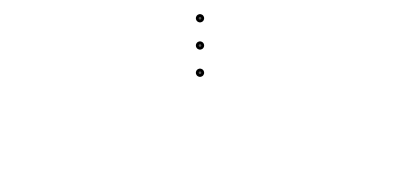

```mathematica
g1=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,-h*(-1)^n],{n,3,6}];
hole=Table[d[n,0,r,holeFillingColor],{n,{2}}];
baseline={Line[{{0.5,0},{6.5,0}}]};
Join[baseline,arrows1,arrows2,hole]
)]
g2=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,-h*(-1)^n],{n,4,6}];
arrows3=Table[a[n,h*(-1)^n],{n,2,2}];
magnons=Table[rc[n,0,r,magnonFillingColor],{n,2,2}];
hole=Table[d[n,0,r,holeFillingColor],{n,{3}}];
baseline={Line[{{0.5,0},{6.5,0}}]};
Join[baseline,arrows1,arrows2,arrows3,magnons,hole]
)]
g3=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,-h*(-1)^n],{n,5,6}];
arrows3=Table[a[n,h*(-1)^n],{n,2,3}];
magnons=Table[rc[n,0,r,magnonFillingColor],{n,2,3}];
hole=Table[d[n,0,r,holeFillingColor],{n,{4}}];
baseline={Line[{{0.5,0},{6.5,0}}]};
Join[baseline,arrows1,arrows2,arrows3,magnons,hole]
)]
g4=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,-h*(-1)^n],{n,6,6}];
arrows3=Table[a[n,h*(-1)^n],{n,2,4}];
magnons=Table[rc[n,0,r,magnonFillingColor],{n,2,4}];
hole=Table[d[n,0,r,holeFillingColor],{n,{5}}];
baseline={Line[{{0.5,0},{6.5,0}}]};
Join[baseline,arrows1,arrows2,arrows3,magnons,hole]
)]
g5=Graphics[(
eraser={e[3.5,0,3,0.5]};
dots=Table[d[3.5,1.25-n/4,0.025,Black],{n,1,3}];
Join[eraser,dots]
)]
```

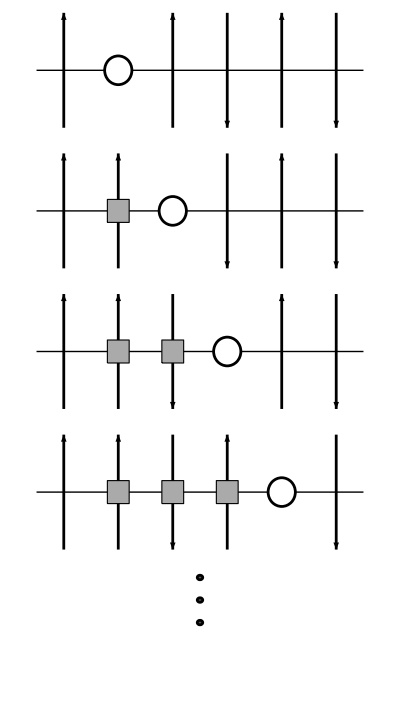

```mathematica
cartoon1=GraphicsGrid[{{g1},{g2},{g3},{g4},{g5}},AspectRatio->1,Spacings->0]
```

```mathematica
(*Export["plots/cartoons2/cartoon1.png",cartoon1,ImageResolution->300]*)
```

-Graphics-

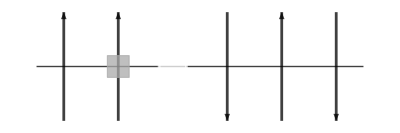

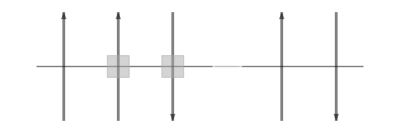

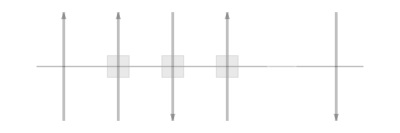

-Graphics-

```mathematica
g1=Graphics[(
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,-h*(-1)^n],{n,3,6}];
hole=Table[d[n,0,r,holeFillingColor],{n,{2}}];
baseline={Line[{{0.5,0},{6.5,0}}]};
Join[baseline,arrows1,arrows2,hole]
)]
g2=Graphics[(
opc=Opacity[0.75];
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,-h*(-1)^n],{n,4,6}];
arrows3=Table[a[n,h*(-1)^n],{n,2,2}];
magnons=Table[rc[n,0,r,magnonFillingColor,{opc}],{n,2,2}];
hole=Table[d[n,0,r,holeFillingColor,{Thickness[0.005],opc}],{n,{3}}];
baseline={opc,Line[{{0.5,0},{6.5,0}}]};
Join[baseline,arrows1,arrows2,arrows3,magnons,hole]
)]
g3=Graphics[(
opc=Opacity[0.5];
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,-h*(-1)^n],{n,5,6}];
arrows3=Table[a[n,h*(-1)^n],{n,2,3}];
magnons=Table[rc[n,0,r,magnonFillingColor,{opc}],{n,2,3}];
hole=Table[d[n,0,r,holeFillingColor,{Thickness[0.005],opc}],{n,{4}}];
baseline={opc,Line[{{0.5,0},{6.5,0}}]};
Join[baseline,arrows1,arrows2,arrows3,magnons,hole]
)]
g4=Graphics[(
opc=Opacity[0.25];
arrows1=Table[a[n,-h*(-1)^n],{n,1,1}];
arrows2=Table[a[n,-h*(-1)^n],{n,6,6}];
arrows3=Table[a[n,h*(-1)^n],{n,2,4}];
magnons=Table[rc[n,0,r,magnonFillingColor,{opc}],{n,2,4}];
hole=Table[d[n,0,r,holeFillingColor,{Thickness[0.005],opc}],{n,{5}}];
baseline={opc,Line[{{0.5,0},{6.5,0}}]};
Join[baseline,arrows1,arrows2,arrows3,magnons,hole]
)]
g5=Graphics[(
opc=Opacity[0.25];
eraser={opc,e[3.5,0,3,0.5]};
dots=Table[d[3.5,1.25-n/4,0.025,Black,{opc}],{n,1,3}];
Join[eraser,dots]
)]
```

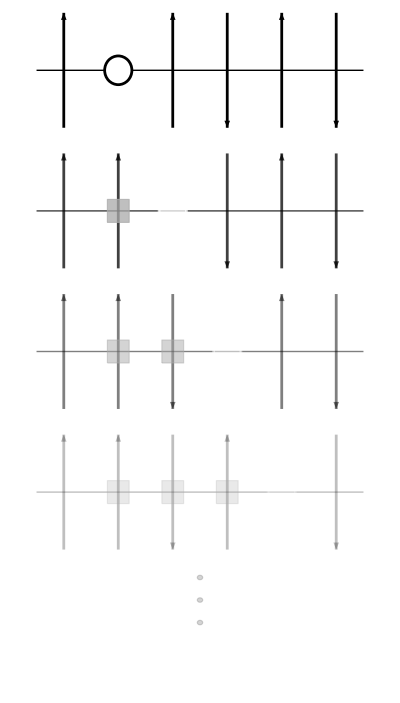

```mathematica
cartoon0=GraphicsGrid[{{g1},{g2},{g3},{g4},{g5}},AspectRatio->1,Spacings->0]
```

```mathematica
(*Export["plots/cartoons2/cartoon0.png",cartoon0,ImageResolution->300]*)
```

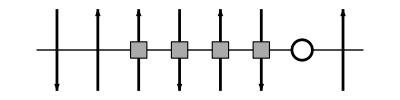

```mathematica
g=Graphics[(
arrows1=Table[a[n,h*(-1)^n],{n,1,2}];
arrows2=Table[a[n,h*(-1)^n],{n,8,8}];
arrows3=Table[a[n,-h*(-1)^n],{n,3,6}];
magnons=Table[rc[n,0,r,magnonFillingColor],{n,3,6}];
hole=Table[d[n,0,r,holeFillingColor],{n,{7}}];
baseline={Line[{{0.5,0},{8.5,0}}]};
Join[baseline,arrows1,arrows2,arrows3,magnons,hole]
)]
```

```mathematica
plt=Labeled[g,MaTeX["n = 4",Magnification->3],Left]
```

-Graphics--Graphics-

```mathematica
Export["plots/cartoon_line.png",plt,ImageResolution->300]
```

plots/cartoon_line.png